## Ugeseddel 1: Simplex

## Opgave 1: plot og simplex

### (a) og (b)

```mathematica
z[x1_,x2_]:=2x1+x2
```

```mathematica
b1[x1_,x2_]:=x2
```

```mathematica
b2[x1_,x2_]:=2x1+5x2
```

```mathematica
b3[x1_,x2_]:=x1+x2
```

```mathematica
b4[x1_,x2_]:=3x1+x2
```

```mathematica
bv={10,60,18,44};
```

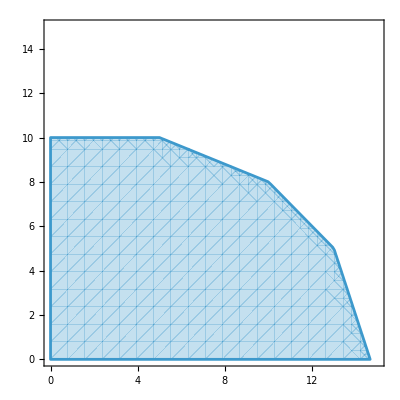

```mathematica
rp = RegionPlot[{
b1[x1,x2]<=bv[[1]]&&
b2[x1,x2]<=bv[[2]]&&
b3[x1,x2]<=bv[[3]]&&
b4[x1,x2]<=bv[[4]]
},{x1,0,15},{x2,0,15}]
```

```mathematica
ContourPlot[{
z[x1,x2]==zl,
b1[x1,x2]==bv[[1]],
b2[x1,x2]==bv[[2]],
b3[x1,x2]==bv[[3]],
b4[x1,x2]==bv[[4]]
},{x1,0,15},{x2,0,15}]
```

```mathematica
Manipulate[
Show[
rp,
ContourPlot[{
z[x1,x2]==zl,
b1[x1,x2]==bv[[1]],
b2[x1,x2]==bv[[2]],
b3[x1,x2]==bv[[3]],
b4[x1,x2]==bv[[4]]
},{x1,0,15},{x2,0,15}],PlotLegends->"Expressions"],
{zl,0,50}]
```

Show::gcomb: Could not combine the graphics objects in 
    Show[rp, -Graphics-, PlotLegends -> Expressions].

Den blå linje er objektfunktionen. Vi kan se at maximum er ved en værdi af objektfunktionen på 31. 
Her skærer bibetingelsen 3 x_1+x_2<=44 bibetingelsen x_1+x_2<=18 hinanden. Hvis vi vi løser ligningerne

3 x_1+x_2=44
x_1+x_2=18

```mathematica
Solve[{3x1+x2==44,x1+x2==18}]
```

{{x1→13,x2→5}}

Ser vi at optimum er når x_1=13 og x_2=5.

### (c)

Vi løser problemet med simplex-metoden.
Vi starter med at opstille tableauet

Derefter køres primal simplex

Det ses at vi får præcis samme løsning.

## Opgave 2: Simplex

### (a)

Her ses det ønskede tableau

Hvor der er indført en slackvariabel for hver bibetingelse.

### (b)

Vi løser problemet med simplex-metoden

Vi ser at den optimale løsning er når (x_1,x_2,x_3)=(0,10,6.67) og her bliver værdien af objektfunktionen Z=70.

## Opgave 3: plot og omskrivning af simplex (ikke løse)

### (a)

For at illustrere problemet, defineres de givne informationer

```mathematica
Clear["Global`*"]
```

```mathematica
z[x1_,x2_]:=5x1+7x2
```

```mathematica
b1[x1_,x2_]:=2x1+3x2
```

```mathematica
b2[x1_,x2_]:=3x1+4x2
```

```mathematica
b3[x1_,x2_]:=x1+x2
```

```mathematica
bv:={42,60,18}
```

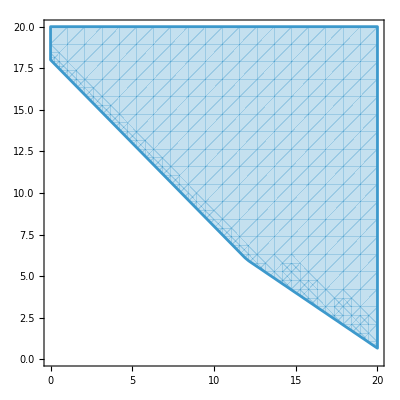

```mathematica
rp=RegionPlot[{
b1[x1,x2]>=bv[[1]]&&
b2[x1,x2]>=bv[[2]]&&
b3[x1,x2]>=bv[[3]]
},{x1,0,20},{x2,0,20}]
```

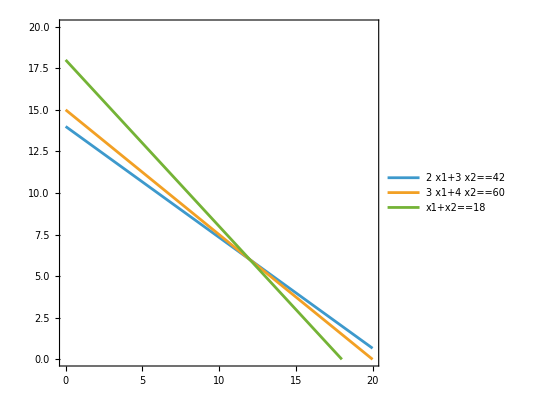

```mathematica
cp=ContourPlot[{
b1[x1,x2]==bv[[1]],
b2[x1,x2]==bv[[2]],
b3[x1,x2]==bv[[3]]
},{x1,0,20},{x2,0,20},PlotLegends->"Expressions"]
```

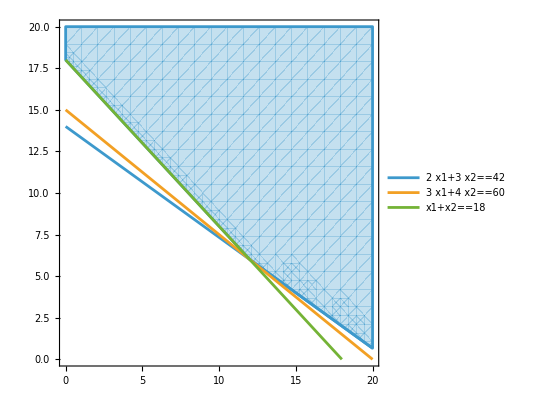

```mathematica
Show[rp,cp]
```

Ud fra vores skitse, kan vi se at bibetingelsen 3 x_1+4 x_2>=60 er overflødig. Den bidrager ikke med noget ny information, da den aldrig er aktiv alene. Denne kan vi altså med fordel smide væk, eftersom problemet ville være det samme, hvis denne ikke var der.

### (c)

Ved at gange objektivfunktionen med minus et, kan vi omdanne problemet fra et minimeringsproblem, til et maksimeringsproblem. Det samme kan vi gøre for bibetingelserne, så de passer i simplex algoritmen. Da bliver problemet

max -4 x_1-7 x_2
u.b.b
-2 x_1-3 x_2<=-42
-3 x_1-4 x_2<=-60
-x_1-x_2<=-18
x_1,x_2>=0

### (d)

Vi ser at objektiv koefficienterne alle er negative, hvormed de vil være positive, ligeså snart de kommer ind tableauet, og det vil ligne at vi befinder os i en optimal løsning med det samme. Derudover er (0,0) ikke inkluderet som en BFS, og dermed vil vi starte vores algoritme uden for mulighedsområdet, hvilket ikke vil virke for simplex algoritmen.

## Opgave 4: formulering af betingelser og simplex

### (a)

Vi definerer to beslutningsvariable, en for hver produkttype. 
x_1=mængde af produkttype 1
x_2=mængde af produkttype 2
Vi ved at profitten er givet ved 1 krone for produkt 1 og 2 kroner for produkt 2. Dermed bliver objektiv funktionen z=x_1+2 x_2 hvor z måler profit i kroner.

### (b) og (c)

Her ses en oversigt over rescourcebrug for de forskellige produkttyper, samt mængden er rescourcer til rådighed

Rescourceforbrug/Produkttype | x_1 | x_2 | Kapacitet
Rescource 1 | 1 | 3 | 200
Rescource 2 | 2 | 2 | 300

Derudover kan der maksimalt sælges 60 enheder af produkt 2. Da bliver bibetingelserne

x_1+3 x_2<=200
2 x_1+2 x_2<=300⟹x_1+x_2<=150
x_2<=60

### (d)

Vi får det samlede maksimeringsproblem

max x_1+2 x_2
u.b.b
x_1+3 x_2<=200
x_1+x_2<=150
x_2<=60
x_1,x_2>=0

Vi løser problemet med simplex.
Her ses tableauet

Vi løser med simplex

Her ses løsningstableuaet

Vi ser at den optimale værdi for objektivfunktionen er 175. Her produceres 125 enheder af x_1 og 25 enheder af x_2. Desuden ser vi at tredje bibetingelse ikke er aktiv.

## Opgave 5: simplex med opstillelse af problem

### (a)

For at opsætte modellen, starter vi med at danne os et overblik. Vi har beslutningsvariablene
bulk carrier =x_1->salgspris 120 mio. euro
RORO ship =x_2-> salgspris 200 mio. euro
container ship=x_3-> sallgspris 260 mio. euro
Vi laver desuden en oversigt over hvor rescourcebrug og kapacitet for de forskellige beslutningsvariable

Rescource/skipstype | x_1 | x_2 | x_3 | Kapacitet
B1: Docks | 1 | 1 | 1 | 11
B2: Labour | 30 | 15 | 45 | 300
B3: Kapital | 40 | 80 | 120 | 820

Man kan ikke producerer negative mængder, hvilket også indsættes i modellen. Dermed har vi følgende model

max 120 x_1+200 x_2+260 x_3
u.b.b
x_1+x_2+x_3<=11
30 x_1+15 x_2+45 x_3<=300
40 x_1+80 x_2+120 x_3<=820
x_1,x_2,x_3>=0

Vi har antaget at kan gange op i bibetinglser og salg uden at de påvirker mængden man benytter. Alt er altså perfekt skalerbart.  Vi har antaget at man ikke kan producere negative mængder. Vi har antaget divisibilitet og perfekt viden. Vi har antaget at både begrænsninger og objektivfunktionen bare er linearkombinationer. Vi har antaget at man godt kan bygge halve skibe (kontinuitet).

### (b)

Vi løser problemet med simplex. Her opstilles tableauet

Derefter gøres simplexalgoritmen

Da fås følgende løsningstableau

Vi ser at løsningen bliver når (x_1,x_2,x_3)=(1.5,9.5,0), og her bliver værdien af objektivfunktionen 2080.

## Ugeseddel 2: Dual simplex og sensitivitet

## Opgave 2

Vi opskriver først problemet

Max              | 4 x_1+2 x_2+5 x_3
U.B.B | -5 x_1-4 x_2-3 x_3>=-11
  | 2 x_1+x_2+3 x_3=8
  | x_1,x_2,x_3>=0

Vi omskriver

-5 x_1-4 x_2-3 x_3>=-11⟹5 x_1+4 x_2+3 x_3<= 11
2 x_1+x_2+3 x_3=8⟹Piecewise[{{2 x_1+x_2+3 x_3>=8⟹-2 x_1-x_2-3 x_3<=-8, }, {2 x_1+x_2+3 x_3<=8, }}]

Dermed bliver problemet

Max              | 4 x_1+2 x_2+5 x_3
U.B.B | 5 x_1+4 x_2+3 x_3<= 11
  | -2 x_1-x_2-3 x_3<=-8
  | 2 x_1+x_2+3 x_3<=8
  | x_1,x_2,x_3>=0

Derefter løser vi problemet med simplex metoden